# 29: Shifted QR Algorithm

This (with some bells and whistles) is what almost all dense eigenvalue algorithms are based on after a preliminary reduction to upper Hessenberg (tridiagonal for symmetric) form. We are going to look at the scheme first and then work out why it works.

Real world versions of QR eigenvalue algorithms do more than one shift at a time and these shifts are implemented implicitly.

## Double Shift

Double shifts are vitally important for real but non-symmetric matrices because of the complex eigenvalue pairs.  A single real shift can not approximate a complex conjugate eigen pair!  To work out how to do this we need to manually work through two steps of QR to see what is actually happening
	H | - | μ_1 I | = | Q_1.R_1 |   |  
  |   | H_1 | = | R_1.Q_1 | + | μ_1 I
H_1 | - | μ_2 I | = | Q_2.R_2 |   |  
  |   | H_2 | = | R_2.Q_2 | + | μ_2 I

Remember each QR step does not change the eigen values since
	  | H-μ_1 I | = | Q_1.R_1
⟹ | (Q_1)ᵀ.(H-μ_1 I) | = | R_1
⟹ | (Q_1)ᵀ.(H-μ_1 I).Q_1 | = | R_1.Q_1
⟹ | (Q_1)ᵀ.(H-μ_1 I).Q_1 | = | H_1-μ_1 I
and for the same reasons
	(Q_2)ᵀ.(H_1-μ_2 I).Q_2 | = | H_2-μ_2 I.

The question is what does this look like if we try to combine the two steps. One way to think about this would be to look at the combined orthogonal matrices Q=Q_1.Q_2 (still orthogonal) and the combined upper triangular matrices R=R_2.R_1(still upper triangular)   
	Q.R=(Q_1.Q_2).(R_2.R_1)
A direct computation gives 
	  | (Q_1.Q_2).(R_2.R_1) | = | Q_1.(Q_2.R_2).R_1
⟹ |   | = | Q_1.(H_1-μ_2 I).R_1
⟹ |   | = | Q_1.((R_1.Q_1 | + | μ_1 I)-μ_2 I).R_1
⟹ |   | = | (Q_1.R_1.Q_1+(μ_1-μ_2)Q_1).R_1
⟹ |   | = | (Q_1.R_1+(μ_1-μ_2)I).Q_1.R_1
⟹ |   | = | ((H-μ_1 I)+(μ_1-μ_2)I).(H-μ_1 I)
⟹ |   | = | (H-μ_2 I).(H-μ_1 I)
In words, the effect of the double step with the two shifts is described by the matrix quadratic
	(H-μ_2 I).(H-μ_1 I)
which is real if μ_1 are the roots of a real polynomial or eigenvalues of a real matrix!  It should be possible to do the double step in real arithmetic if μ_1 and μ_2 are real (no surprise there) or a complex conjugate pair!

We could build the matrix (H-μ_2 I).(H-μ_1 I), compute a QR decomposition of it and reverse the order but we do not need to.  It turns out that although there are many different Hessenberg reductions of a matrix A ones with the same first column are essentially the same.  This is going to let us compute the two step reduction without forming the quadratic matrix.  This clever trick is called an implicit shift.

## Implicit Shifts

The first column of (H-μ_2 I).(H-μ_1 I) is simply m=(H-μ_2 I).(H-μ_1 I).e_1.  Since H is Upper Hessenberg m has three non-zero entries at the top. A direct computation gives
	m_1 | = | H_(1,1)H_(1,1) | + | H_(1,2)H_(2,1) | - | (μ_1+μ_2)H_(1,1) | + | μ_1 μ_2
m_2 | = | H_(2,1)H_(1,1) | + | H_(2,2)H_(2,1) | - | (μ_1+μ_2)s |   |  
m_3 | = | H_(3,2)H_(2,1) |   |   |   |   |   |

The standard formulas give a Householder reduction of m to e_1.

## Motivational Demo

The book says “Compute the QR decomposition, flip the order of the factors and repeat!”. Here is an example for a symmetric matrix.

```mathematica
m=7; MaxIter=22;
A=RandomReal[{-1,1},{m,m}]; A=A+Aᵀ;
T0=T=Chop[HessenbergDecomposition[A]⟦2⟧];
TabView[
Table[
{Q,R}=QRDecomposition[T];Q=Qᵀ;
T=Chop[R.Q];
MatrixPlot[T],
{MaxIter}]
]
```

12345678910111213141516171819202122

Lets look at the first and last “T” matrices

```mathematica
TabView[{
"T_0"->MatrixForm[T0],
"T_-1"->MatrixForm[T]}]
Eigenvalues[A]
```

12

{-3.20684,2.84986,-2.11601,1.82991,1.53912,-1.01371,0.52521}

It is pretty clear that something is driving the off-diagonals to zero: this means the diagonals are heading to the eigenvalues!  We want to understand what is doing this. Once we understand that we might be able to make it go faster! In a fit of bravado, we are going to guess at something that makes it go faster

### Shifts

After a few steps I have a vague idea of some of the eigenvalues! There should be a way of incorporating these estimates into the algorithm.

Obvious Fact #42:
If the eigenvalues of A are {λ_1,λ_2,…,λ_m} then the eigenvalues of A-μ I_m are simply {λ_1-μ,λ_2-μ,…,λ_m-μ}
This is called a shift.

Less Obvious Observation:
If μ is an eigenvalue then one QR step on “T-μ I_m" makes the problem gets smaller. 
This is called “Deflation”.

{2.44012,1.28022,-3.86877,-0.179029,-2.72121,-0.905731,-1.56584}

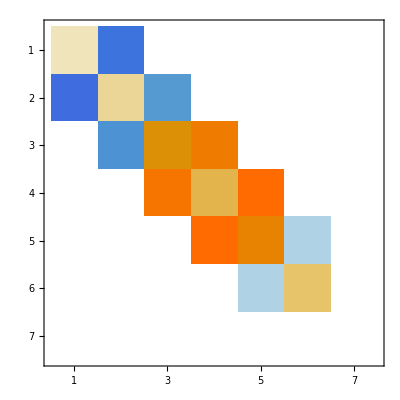

```mathematica
m=7; MaxIter=22;
A=RandomReal[{-1,1},{m,m}]; A=A+Aᵀ;
λs=Eigenvalues[A];
T0=T=Chop[HessenbergDecomposition[A]⟦2⟧];
μ=RandomChoice[λs];
{Q,R}=QRDecomposition[T-μ IdentityMatrix[m]];Q=Qᵀ;
T=Chop[R.Q];
Eigenvalues[T]+μ
MatrixPlot[T]
```

It does not have to be exact to be useful! The cheesiest guess we have at an eigenvalue is the last diagonal entry! Even this simple “shift” strategy helps a lot.

```mathematica
m=7; MaxIter=22;
A=RandomReal[{-1,1},{m,m}]; A=A+Aᵀ;
λs=Eigenvalues[A];
T0=T=Chop[HessenbergDecomposition[A]⟦2⟧];
μ=T⟦m,m⟧;
{Q,R}=QRDecomposition[T-μ IdentityMatrix[m]];Q=Qᵀ;
T=Chop[R.Q];
TabView[{
"T_0"->MatrixPlot[T0],
"T_1"->MatrixPlot[T]}]
TabView[{
"T_0"->MatrixForm[T0],
"T_1"->MatrixForm[T]}]
```

12

12

I guess we should throw this into our code and see if it is faster! The one missing ingredient is that we need to add the shift back in if we want to combine steps. Here is our new code!

```mathematica
m=7; MaxIter=4;
A=RandomReal[{-1,1},{m,m}]; A=A+Aᵀ;
T0=T=Chop[HessenbergDecomposition[A]⟦2⟧];
Id=IdentityMatrix[m];
TabView[
Table[
μ=T⟦m,m⟧;
{Q,R}=QRDecomposition[T-μ Id];Q=Qᵀ;
T=Chop[R.Q+ μ Id];
MatrixPlot[T],
{MaxIter}]
]
MatrixForm[T]
```

1234

(-0.893483 | -2.97 | 0 | 0 | 0 | 0 | 0
-2.97 | 2.29949 | -0.300737 | 0 | 0 | 0 | 0
0 | -0.300737 | 1.07068 | -2.19765 | 0 | 0 | 0
0 | 0 | -2.19765 | 0.223879 | -0.139886 | 0 | 0
0 | 0 | 0 | -0.139886 | 1.98201 | -0.0078356 | 0
0 | 0 | 0 | 0 | -0.0078356 | 0.453441 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.730142)

It almost always immediately resolves an eigenvalue at the bottom corner!  Of course, the shift stops doing any good once that has happened! If we want to continue effectively we need to work out how to “deflate” the converged elements. In general, deflation involves slightly complicated bookkeeping. Our book wimps out on “deflation”. I am going to try to show what happens when the bottom deflates!

### Deflation

Lets decide that the bottom diagonal “eigenvalue” is resolved when the ratio of the off-diagonal element to the diagonal element is less than some tolerance.  Our bookkeeping consists of a single number “n” that is the number of eigenvalues still to be resolved. I am going to call this the active dimension.  Of course, n starts at m and the code decreases it as appropriate.

```mathematica
$MachineEpsilon
```

2.22045×10^-16

```mathematica
m=8; MaxIter=12;
A=RandomReal[{-1,1},{m,m}]; A=A+Aᵀ;
T0=T=Chop[HessenbergDecomposition[A]⟦2⟧];
(* Initialize the Active Dimension *)
n=m;
Tol=10^-10;
TabView[
Table[
If[ Abs[T⟦n-1,n⟧]/(Abs[T⟦n,n⟧]+$MachineEpsilon)<Tol,n=n-1] ;
Id=IdentityMatrix[n];
μ=T⟦n,n⟧;
{Q,R}=QRDecomposition[T⟦1;;n,1;;n⟧-μ Id];Q=Qᵀ;
T⟦1;;n,1;;n⟧=Chop[R.Q+ μ Id];
MatrixPlot[T],
{MaxIter}]
]
MatrixForm[T]
Eigenvalues[A]
```

123456789101112

(2.89761 | 0.559399 | 0 | 0 | 0 | 0 | 0 | 0
0.559399 | -5.07727 | 1.17454 | 0 | 0 | 0 | 0 | 0
0 | 1.17454 | 1.7954 | -0.0476736 | 0 | 0 | 0 | 0
0 | 0 | -0.0476736 | 1.44049 | 1.09737×10^-6 | 0 | 0 | 0
0 | 0 | 0 | 1.09737×10^-6 | -3.00552 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -2.10657 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -0.656371 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.1925)

{-5.30958,-3.00552,2.94351,-2.10657,1.98583,1.43646,-1.1925,-0.656371}

### Better Shift

This simplest shift does not always work!  For instance, the tridiagonal matrix 
	T=(2 | 0 |  
0 | 0 | 1
  | 1 | 0)
is unchanged by an unshifted QR step!

```mathematica
T=({{2, 0, 0}, {0, 0, 1}, {0, 1, 0}});
{Q,R}=QRDecomposition[T];Q=Qᵀ;
MatrixForm[R.Q]
```

(2 | 0 | 0
0 | 0 | 1
0 | 1 | 0)

Clearly adding a shift of μ=T_(3,3)=0 does not change the situation. The problem is that the bottom two eigenvalues are ±1 and our current algorithm can not resolve the symmetry.  The solution called a Wilkinson shift is to choose the eigenvalue of the bottom 2×2 matrix nearest the bottom entry.

Here is a demo of the “bad” matrix breaking the Rayleigh shift.

```mathematica
m=3; MaxIter=4;
T0=T=N[({{2, 0, 0}, {0, 0, 1}, {0, 1, 0}})];
(* Initialize the Active Dimension *)
n=m;
Tol=10^-10;
TabView[
Table[
If[ Abs[T⟦n-1,n⟧]/(Abs[T⟦n,n⟧]+$MachineEpsilon)<Tol,n=n-1] ;
Id=IdentityMatrix[n];
μ=T⟦n,n⟧;
{Q,R}=QRDecomposition[T⟦1;;n,1;;n⟧-μ Id];Q=Qᵀ;
T⟦1;;n,1;;n⟧=Chop[R.Q+ μ Id];
MatrixPlot[T],
{MaxIter}]
]
MatrixForm[T]
```

1234

(2. | 0 | 0
0 | 0 | 1.
0 | 1. | 0)

Here is the Wilkinson shift code

```mathematica
m=3; MaxIter=3;
T0=T=N[({{2, 0, 0}, {0, 0, 1}, {0, 1, 0}})];
(* Initialize the Active Dimension *)
n=m;
Tol=10^-10;
TabView[
Table[
If[ Abs[T⟦n-1,n⟧]/(Abs[T⟦n,n⟧]+$MachineEpsilon)<Tol,n=n-1] ;
Id=IdentityMatrix[n];
(* Wilikinson Shift *)
If[n>1,
{μ1,μ2}=Eigenvalues[T⟦n-1;;n,n-1;;n⟧];
μ=Sort[ {μ1,μ2}, Abs[#1-T⟦n,n⟧]≤Abs[#2-T⟦n,n⟧]&]⟦1⟧,
μ=T⟦n,n⟧];
{Q,R}=QRDecomposition[T⟦1;;n,1;;n⟧-μ Id];Q=Qᵀ;
T⟦1;;n,1;;n⟧=Chop[R.Q+ μ Id];
MatrixPlot[T],
{MaxIter}]
]
MatrixForm[T]
```

123

(2. | 0 | 0
0 | 1. | 0
0 | 0 | -1.)

### Racing Shifts

We have two different shifts: Wilkinson and Rayleigh.  The obvious question is which is faster.  easy enough to answer with our assorted code fragments.

```mathematica
m=23; MaxIter=18;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
T0=Chop[HessenbergDecomposition[A]⟦2⟧];
(* Initialize the Active Dimension *)
n=m; T=T0; Tol=10^-12;
Wilkinson =TabView[
Table[
If[ Abs[T⟦n-1,n⟧]/(Abs[T⟦n,n⟧]+$MachineEpsilon)<Tol,n=n-1] ;
Id=IdentityMatrix[n];
(* Wilikinson Shift *)
If[n>1,
{μ1,μ2}=Eigenvalues[T⟦n-1;;n,n-1;;n⟧];
μ=Sort[ {μ1,μ2}, Abs[#1-T⟦n,n⟧]≤Abs[#2-T⟦n,n⟧]&]⟦1⟧,
μ=T⟦n,n⟧];
{Q,R}=QRDecomposition[T⟦1;;n,1;;n⟧-μ Id];Q=Qᵀ;
T⟦1;;n,1;;n⟧=Chop[R.Q+ μ Id];
MatrixPlot[T],
{MaxIter}],MaxIter];
n=m; T=T0;
Rayleigh =TabView[
Table[
If[ Abs[T⟦n-1,n⟧]/(Abs[T⟦n,n⟧]+$MachineEpsilon)<Tol,n=n-1] ;
Id=IdentityMatrix[n];
(* Rayleigh Shift *)
μ=T⟦n,n⟧;
{Q,R}=QRDecomposition[T⟦1;;n,1;;n⟧-μ Id];Q=Qᵀ;
T⟦1;;n,1;;n⟧=Chop[R.Q+ μ Id];
MatrixPlot[T],
{MaxIter}],MaxIter];
TabView[{
"Rayleigh"->Rayleigh,
"Wilkinson"->Wilkinson
}]
```

12

Wilkinson (almost) always wins.  Rayleigh can stall. Wilkinson is better.